```mathematica
ClearAll[c,G,MSun,rhoRadBBN];

c=29979245800;                   (*velocidad de la luz:cm/s*)
G=66743/10^12;                   (*constante gravitacional:cm^3/(g s^2)*)
MSun=198847*10^28;               (*masa solar:g*)

rhoRadBBN=7331305019814086*10^11;
(*densidad de energía de radiación en BBN:erg/cm^3*)
```

```mathematica
ti=37/50;                       (*coordenada temporal de BBN:0.74 s*)
ai=83/500000000000;             (*factor de escala en BBN:1.66*10^-10*)
Hti=67/100;                     (*parámetro de Hubble en BBN:0.67 s^-1*)
```

```mathematica
ρ0[ξ_]:= ξ*rhoRadBBN
```

```mathematica
Cxi[ξ_]:= (4π G)/(3c^2)*ρ0[ξ]
```

```mathematica
ClearAll[sol];
```

```mathematica
tMin=-5;
(* n = -1 luego 
(Y[t])^((n-1)/2) ----> Y^-1
*)
```

```mathematica
ClearAll[sol,tBounce]
```

```mathematica
sol[ξ_]:=sol[ξ]=Quiet@NDSolve[{Y'[t]==v[t],v'[t]==2*Cxi[ξ]*(Y[t])^(-1),Y[ti]==1,v[ti]==2*Hti,WhenEvent[v[t]==0,"StopIntegration"]},{Y,v},{t,-1,ti},WorkingPrecision->40,AccuracyGoal->20,PrecisionGoal->20,Method->"StiffnessSwitching",MaxSteps->Infinity];
```

```mathematica
tBounce[ξ_]:=tBounce[ξ]=(Y/. sol[ξ][[1]])["Domain"][[1,1]];
```

```mathematica
tB= tBounce[1/10]
```

-0.02689614804598900925653539950031762685982

```mathematica
Yfunc[ξ_,t_]:=Y[t]/. sol[ξ][[1]];
vFunc[ξ_,t_]:=v[t]/. sol[ξ][[1]];
```

```mathematica
apos[ξ_,t_]:=ai*Sqrt[Yfunc[ξ,Abs[t]+tBounce[ξ]]];
```

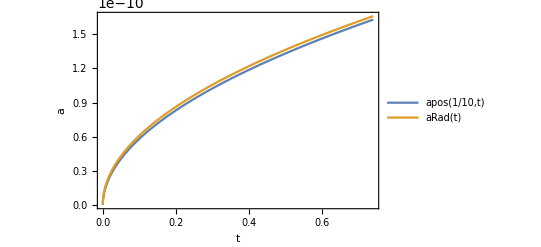

```mathematica
ar := ai/ti^(1/2)
aRad[t_]:= ar*t^(1/2)
Plot[{apos[1/10, t],aRad[t]},{t,0,ti},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0, PlotLegends->"Expressions"]
```

```mathematica
ρbh[ξ_,t_]:= ρ0[ξ]*(ai/apos[ξ, t])^4
```

```mathematica
ρbh[1/10,0]
```

9.17416390067523272064124287609164×10^42

```mathematica
ρbh[1/10, 10^(-4)]
```

8.65608730193589208385778364740664768×10^33

```mathematica
DotA[ξ_,t_]:=Sign[t]*(ai^2*vFunc[ξ,Abs[t]+tBounce[ξ]])/(2*apos[ξ,t]);
```

```mathematica
DotA[1/10, 0]
```

0

```mathematica
ρrad[ξ_, t_]:= (3c^2)/(8π G)(DotA[ξ, t]/apos[ξ, t])^2 -ρbh[ξ, t]
```

```mathematica
ρrad[1/10, 10^(-4)]
```

3.63161564521683026639517071543315322×10^34

```mathematica
ρrad[1/10, 0]
```

-9.17416390067523272064124287609164×10^42

```mathematica
HubbleParameter[ξ_, t_]:= √((8π G)/(3c^2)(ρrad[ξ, t]+ρbh[ξ, t]))
```

```mathematica
HubbleParameter[1/10, 0]
```

0.

```mathematica
HubbleParameter[1/10, 10^(-4)]
```

5289.48925616011874431310603838474247

```mathematica
5289.5069196841113186285097189208109531727050978632872936576626`36.94221135751255/5000
```

1.05790138393682226372570194378416219

```mathematica
MHubble[ξ_, t_]:= (4π c)/3*(ρrad[ξ, t]+ρbh[ξ, t])/(HubbleParameter[ξ, t])^3
```

```mathematica
γ := 0.2
Minic[ξ_, t_] := γ*MHubble[ξ, t]
```

```mathematica
Minic[1/10, 10^(-4)]
```

7.63208×10^33

```mathematica
Minic[1/10,10^(-4)]/MSun
```

3.83816

```mathematica
β = ρbh[1/10, 10^(-4)]/(ρrad[1/10, 10^(-4)]+ρbh[1/10, 10^(-4)])
```

0.19247621598034970645984251565259529

```mathematica
xiCompareValues=10^-Range[10];
```

```mathematica
tForm=10^(-4);
```

```mathematica
tablaDatos=N[Table[{xi,HubbleParameter[xi,tForm],MHubble[xi,tForm],Minic[xi,tForm],Minic[xi,tForm]/MSun, ρbh[xi,tForm]/(ρrad[xi,tForm]+ρbh[xi,tForm])},{xi,xiCompareValues}],18];
```

```mathematica
datos= Grid[Prepend[tablaDatos,{"ξ","H","\!\(\*SubscriptBox[\(M\), \(H\)]\)","\!\(\*SubscriptBox[\(M\), \(inic\)]\)","\!\(\*SubscriptBox[\(M\), \(inic\)]\)[MSun]", "β"}],Frame->All,Background->{None,{LightGray,None}},Alignment->Left]
```

ξ | H | M_H | M_inic | M_inic[MSun] | β
0.1 | 5289.48925616011874 | 3.816037643018726×10^34 | 7.63208×10^33 | 3.83816 | 0.192476215980349706
0.01 | 5013.42767183978683 | 4.02616561663546395×10^34 | 8.05233×10^33 | 4.04951 | 0.0106440614848725685
0.001 | 5001.27683633873667 | 4.0359473739163777×10^34 | 8.07189×10^33 | 4.05935 | 0.00102067425361944038
0.0001 | 5000.12708721002603 | 4.03687541572326536×10^34 | 8.07375×10^33 | 4.06028 | 0.000101650941841227084
0.00001 | 5000.01277001186319 | 4.03696771234491116×10^34 | 8.07394×10^33 | 4.06038 | 0.0000101609490230702005
1.×10^-6 | 5000.00127372351556 | 4.03697699437152085×10^34 | 8.07395×10^33 | 4.06039 | 1.01605349295314888×10^-6
1.×10^-7 | 5000.00012711284343 | 4.03697792013967829×10^34 | 8.07396×10^33 | 4.06039 | 1.01604935119555415×10^-7
1.×10^-8 | 5000.00001270093696 | 4.0369780125153461×10^34 | 8.07396×10^33 | 4.06039 | 1.01604893694862019×10^-8
1.×10^-9 | 5000.00000127061168 | 4.03697802174414046×10^34 | 8.07396×10^33 | 4.06039 | 1.0160488955206372×10^-9
1.×10^-10 | 5000.00000012707751 | 4.03697802266742493×10^34 | 8.07396×10^33 | 4.06039 | 1.01604889137798796×10^-10

```mathematica
formationHeaders = {"ξ", "H(t_form)","MHubble","Minic [g]", "Minic [Msun]", "β"};
```

```mathematica
csvPath=FileNameJoin[{NotebookDirectory[],"tabla_formacion_nm1.csv"}];
```

```mathematica
Export[csvPath,Prepend[tablaDatos,formationHeaders],"CSV"]
```

/home/iara/doctorado/tres incognitas/tabla_formacion_nm1.csv